```mathematica
left[f_, point_, delta_]:=
(f[point]-f[point-delta])/delta
```

```mathematica
central[f_, point_, delta_]:=
(f[point+delta]-f[point-delta])/(2*delta)
```

```mathematica
right[f_, point_, delta_]:=
(f[point+delta]-f[point])/delta
```

```mathematica
(*Часть 1*)
```

```mathematica
(*1*)
```

```mathematica
f1[x_]:= x^2
```

```mathematica
(*точная и левая*)
```

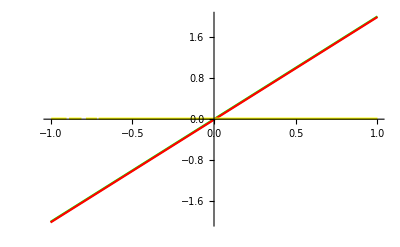

```mathematica
Show[Plot[f1'[x], {x, -1, 1}, PlotStyle->Green], Plot[left[f1, x, 0.01], {x, -1, 1}, PlotStyle->Red], Plot[f1'[x]-left[f1, x, 0.01], {x, -1, 1}, PlotStyle->Yellow]]
```

```mathematica
(*точная и центральная*)
```

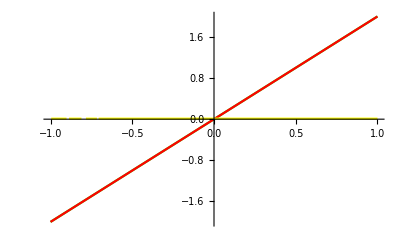

```mathematica
Show[Plot[f1'[x], {x, -1, 1}, PlotStyle->Green], Plot[central[f1, x, 0.01], {x, -1, 1}, PlotStyle->Red], Plot[f1'[x]-left[f1, x, 0.01], {x, -1, 1}, PlotStyle->Yellow]]
```

```mathematica
(*точная и правая*)
```

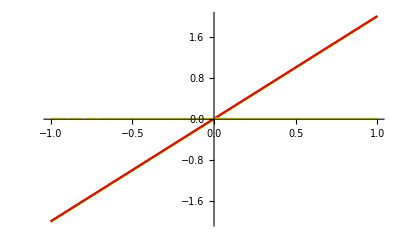

```mathematica
Show[Plot[f1'[x], {x, -1, 1}, PlotStyle->Green], Plot[right[f1, x, 0.01], {x, -1, 1}, PlotStyle->Red], Plot[f1'[x]-left[f1, x, 0.01], {x, -1, 1}, PlotStyle->Yellow]]
```

```mathematica
(*точность хорошая, у центральной вроде бы самая хорошая*)
```

```mathematica
(*2*)
```

```mathematica
f2[x_]:=x^3
```

```mathematica
(*точная и левая*)
```

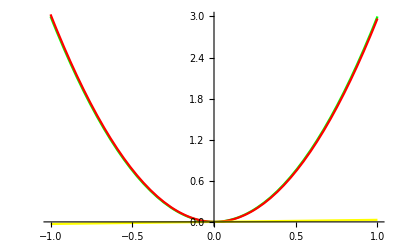

```mathematica
Show[Plot[f2'[x], {x, -1, 1}, PlotStyle->Green], Plot[left[f2, x, 0.01], {x, -1, 1}, PlotStyle->Red], Plot[f2'[x]-left[f2, x, 0.01], {x, -1, 1}, PlotStyle->Yellow]]
```

```mathematica
(*точная и центральная*)
```

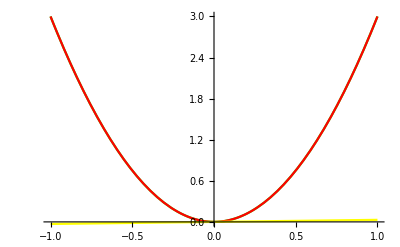

```mathematica
Show[Plot[f2'[x], {x, -1, 1}, PlotStyle->Green], Plot[central[f2, x, 0.01], {x, -1, 1}, PlotStyle->Red], Plot[f2'[x]-left[f2, x, 0.01], {x, -1, 1}, PlotStyle->Yellow]]
```

```mathematica
(*точная и правая*)
```

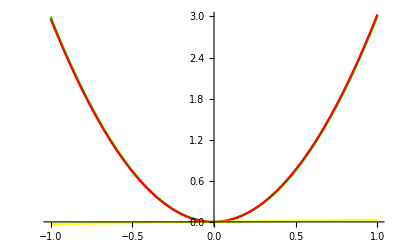

```mathematica
Show[Plot[f2'[x], {x, -1, 1}, PlotStyle->Green], Plot[right[f2, x, 0.01], {x, -1, 1}, PlotStyle->Red], Plot[f2'[x]-left[f2, x, 0.01], {x, -1, 1}, PlotStyle->Yellow]]
```

```mathematica
(*точность настолько хорошая, что это скучно*)
```

```mathematica
(*3*)
```

```mathematica
f3[x_]:=x^4
```

```mathematica
(*точная и левая*)
```

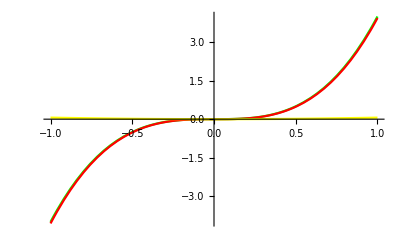

```mathematica
Show[Plot[f3'[x], {x, -1, 1}, PlotStyle->Green], Plot[left[f3, x, 0.01], {x, -1, 1}, PlotStyle->Red], Plot[f3'[x]-left[f3, x, 0.01], {x, -1, 1}, PlotStyle->Yellow]]
```

```mathematica
(*точная и центральная*)
```

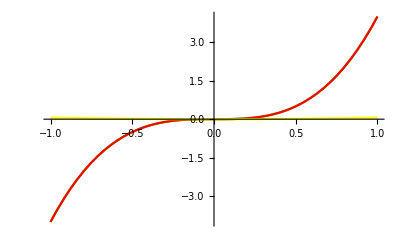

```mathematica
Show[Plot[f3'[x], {x, -1, 1}, PlotStyle->Green], Plot[central[f3, x, 0.01], {x, -1, 1}, PlotStyle->Red], Plot[f3'[x]-left[f3, x, 0.01], {x, -1, 1}, PlotStyle->Yellow]]
```

```mathematica
(*точная и правая*)
```

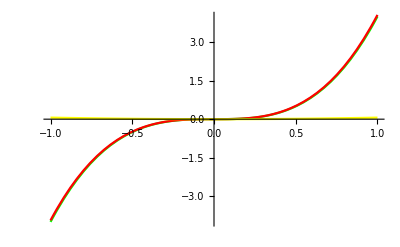

```mathematica
Show[Plot[f3'[x], {x, -1, 1}, PlotStyle->Green], Plot[right[f3, x, 0.01], {x, -1, 1}, PlotStyle->Red], Plot[f3'[x]-left[f3, x, 0.01], {x, -1, 1}, PlotStyle->Yellow]]
```

```mathematica
(*для интереса сделаем шаг побольше*)
```

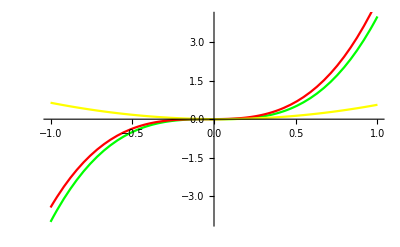

```mathematica
Show[Plot[f3'[x], {x, -1, 1}, PlotStyle->Green], Plot[right[f3, x, 0.1], {x, -1, 1}, PlotStyle->Red], Plot[f3'[x]-left[f3, x, 0.1], {x, -1, 1}, PlotStyle->Yellow]]
```

```mathematica
(*все работает и центральная производная как обычно лучше всех*)
```

```mathematica
newton[f_,x00_,  eps_:0.01]:=Module[{df, x0=x00, xn, i=0},
df=central[f, x0, 0.01];
xn = x0 - f[x0]/df;
While[Abs[xn-x0]>eps, 
x0=xn;
df=central[f, x0, 0.01];
xn=x0-f[x0]/df;
i++;];
Return [N[xn]]]
```

```mathematica
(*ньютон кто*)
```

```mathematica
f4[x_]:= Log[x]+x^2
```

```mathematica
Solve[ Log[x]+x^2==0]//N
```

{{x→0.652919}}

```mathematica
newton[ f4, 1, 0.01]
```

0.652919

```mathematica
(*работает*)
```

```mathematica
(*Часть 2*)
```

```mathematica
(*формула второй производной*)
```

```mathematica
(*1*)
```

```mathematica
centralDD[f_, point_, delta_]:=(f[point+2*delta]-2*f[point]+f[point-2*delta])/(4*delta^2)
```

```mathematica
centralDD[Cos, -8/5Pi, 0.001]//N
```

-0.309017

```mathematica
D[D[Cos[x], x],x]
```

-Cos[x]

```mathematica
-Cos[-8/5Pi]//N
```

-0.309017

```mathematica
(*формула центральной второй производной работает*)
```

```mathematica
(*2*)
```

```mathematica
f5[x_]:=x^2+x^3
```

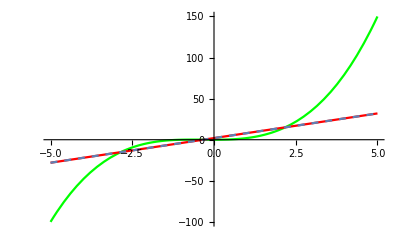

```mathematica
Show[Plot[f5[x], {x, -5, 5}, PlotStyle->Green], Plot[centralDD[f5, x, 0.1], {x, -5, 5}, PlotStyle->Red], Plot[f5''[x], {x, -5, 5}, PlotStyle->Dashed]]
```

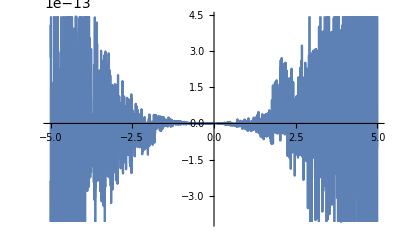

```mathematica
Plot[centralDD[f5, x, 0.1]-f5''[x],{x, -5, 5}]
```

```mathematica
(*точность практически идеальная*)
```

```mathematica
f6[x_]:=Log[x]*x^2
```

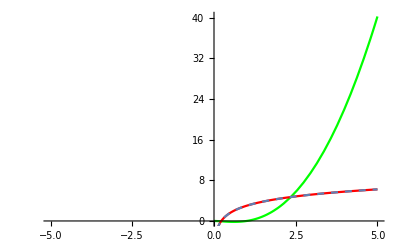

```mathematica
Show[Plot[f6[x], {x, -5, 5}, PlotStyle->Green], Plot[centralDD[f6, x, 0.01], {x, -5, 5}, PlotStyle->Red], Plot[f6''[x], {x, -5, 5}, PlotStyle->Dashed]]
```

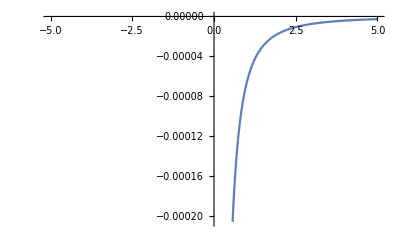

```mathematica
Plot[centralDD[f6, x, 0.01]-f6''[x],{x, -5, 5}]
```

```mathematica
(*точность не очень хорошая вблизи нуля, но становится достаточно маленькой далее*)
```

```mathematica
(*3*)
```

```mathematica
(*проанализируем на примере дифференциирования для функции Log[x^3]*)
```

```mathematica
f7[x_]:=Sin[x^3]
```

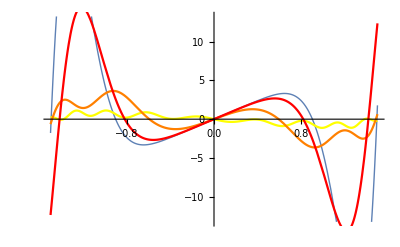

```mathematica
Show[Plot[f7''[x],{x, -1.5, 1.5},PlotStyle->Thick],Plot[centralDD[f7, x, 0.8], {x, -1.5, 1.5}, PlotStyle->Yellow],Plot[centralDD[f7, x, 0.4], {x, -1.5, 1.5}, PlotStyle->Orange],Plot[centralDD[f7, x, 0.2], {x, -1.5, 1.5}, PlotStyle->Red]]
```

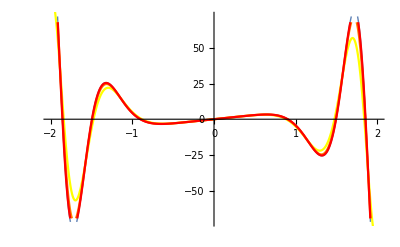

```mathematica
Show[Plot[f7''[x],{x, -2, 2},PlotStyle->Thick],Plot[centralDD[f7, x, 0.1], {x, -2, 2}, PlotStyle->Yellow],Plot[centralDD[f7, x, 0.05], {x, -2, 2}, PlotStyle->Orange],Plot[centralDD[f7, x, 0.025], {x, -2, 2}, PlotStyle->Red]]
```

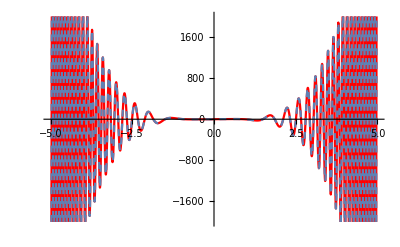

```mathematica
Show[Plot[centralDD[f7, x, 0.001], {x, -5, 5}, PlotStyle->Red],Plot[f7''[x],{x, -5, 5},PlotStyle->Dashed]]
```

```mathematica
(*Можно заметить, что с уменьшением длины шага точность увеличивается, при шаге 0.001 графики почти неразличимы на отрезке от -5 до 5*)
```

```mathematica
(*и часть про метод Ньютона*)
```

```mathematica
(*можно применить для поиска точек экстремума, так как в них производная функции равна нулю, следовательно метод Ньютона ищет эту точку*)
```

```mathematica
(*метод ньютона с использованием центральной переменной*)
```

```mathematica
central[f_, point_, delta_]:=
(f[point+delta]-f[point-delta])/(2*delta)
```

```mathematica
newton[f_,x00_,  eps_:0.01]:=Module[{df, x0=x00, xn, i=0},
df=central[f, x0, 0.01];
xn = x0 - f[x0]/df;
While[Abs[xn-x0]>eps, 
x0=xn;
df=central[f, x0, 0.01];
xn=x0-f[x0]/df;
i++;];
Return [N[xn]]]
```

```mathematica
(*1*)
```

```mathematica
f8[x_]:=(x-1)*(x-2)
```

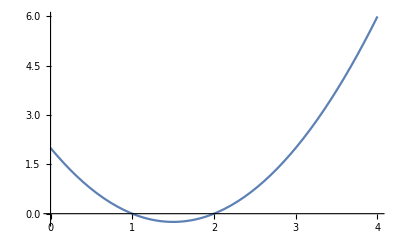

```mathematica
Plot[f8[x], {x, 0,4}]
```

```mathematica
f9[x_]:=central[f8, x, 0.0000001]
```

```mathematica
newton[f9, 1]
```

1.5

```mathematica
Solve[f8'[x]==0]//N
```

{{x→1.5}}

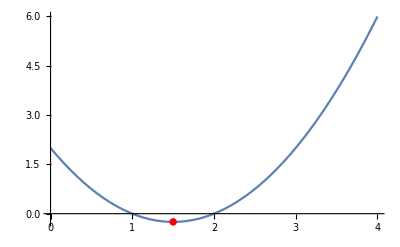

```mathematica
Show[Plot[f8[x], {x, 0,4}],ListPlot[{{newton[f9, 1], f8[newton[f9, 1]]}}, PlotStyle->Red]]
```

```mathematica
(*точка минимума функции имеет абсциссу 1.5, что подтверждает метод Solve*)
```

```mathematica
(*2*)
```

```mathematica
f10[x_]:= x^3 -x+ⅇ^(-x)
```

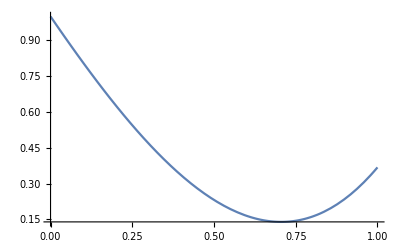

```mathematica
Plot[f10[x], {x, 0,1}]
```

```mathematica
f11[x_]:=central[f10, x, 0.0000001]
```

```mathematica
newton[f11, 0]
```

0.705645

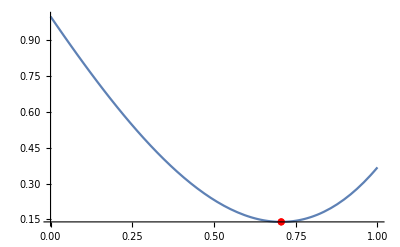

```mathematica
Show[Plot[f10[x], {x, 0,1}],ListPlot[{{newton[f11, 0], f10[newton[f11, 0]]}}, PlotStyle->Red]]
```

```mathematica
(*локальный минимум 0.7053376481999567*)
```

```mathematica
(*3*)
```

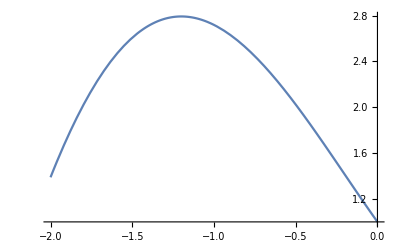

```mathematica
Plot[f10[x], {x, -2, 0}]
```

```mathematica
newton[f11, -1]
```

-1.20003

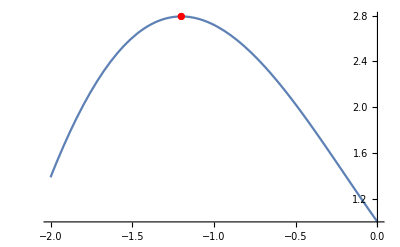

```mathematica
Show[Plot[f10[x], {x, -2, 0}], ListPlot[{{newton[f11, -1], f10[newton[f11, -1]]}}, PlotStyle->Red]]
```

```mathematica
(*локальный максимум -1.2000301386942926*)
```